```mathematica
Guy F. Mongelli, F.E.                                                                              ECHE 462
Prof. R.M. Sankaran                                                                                   4/15/2013
```

```mathematica
Assignment #6
```

```mathematica
Problem 2:
```

```mathematica
ϕ1=.1;
```

```mathematica
ϕ2=1;
```

```mathematica
ϕ3=10;
```

```mathematica
ϕ4=100;
```

```mathematica
The general solution for the irreversible reaction case is:
```

```mathematica
ψ[χ_]=Cosh[ϕ*χ]/Cosh[ϕ];
```

```mathematica
Creating a solution for each of the Thiele modulii:
```

```mathematica
ψ1[χ_]=Cosh[ϕ1*χ]/Cosh[ϕ1];
```

```mathematica
ψ2[χ_]=Cosh[ϕ2*χ]/Cosh[ϕ2];
```

```mathematica
ψ3[χ_]=Cosh[ϕ3*χ]/Cosh[ϕ3];
```

```mathematica
ψ4[χ_]=Cosh[ϕ4*χ]/Cosh[ϕ4];
```

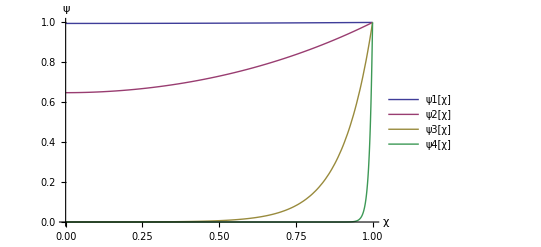

```mathematica
Plot[{ψ1[χ],ψ2[χ],ψ3[χ],ψ4[χ]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ1[χ]", "ψ2[χ]","ψ3[χ]","ψ4[χ]"}]
```

```mathematica
Consideration:  The values of the equilibrium constant to not incorporate into the dimensionless concentration, and therefore evaluating this one case completely explores the system.  Additionally,
```

```mathematica
FOR THE REVERSIBLE CASE:
```

```mathematica
In the infinite k case, the solution collapses into the irreversible k case.
```

```mathematica
Note that the Thiele modulus is deined differently for the reversible case (How does this effect the solution?  If Thiele modulusis constant than either x, or k must change to correct for it).
```

```mathematica
ϕrev=xp*Sqrt[(k/dtae)*((1+k)/k)];
```

```mathematica
Assume that c equals 1 intitially and writing the Thielee modulii for the reversible cases in terms of those for the irreversible cases.  This solution explores the corrected modulii from the initial .1,1,10 and 100 values.
```

```mathematica
ϕ6[k_]=ϕ1*Sqrt[(1+k)/k];
```

```mathematica
ϕ7[k_]=ϕ2*Sqrt[(1+k)/k];
```

```mathematica
ϕ8[k_]=ϕ3*Sqrt[(1+k)/k];
```

```mathematica
ϕ9[k_]=ϕ4*Sqrt[(1+k)/k];
```

```mathematica
coeffs[k_]={ϕ6[k],ϕ7[k],ϕ8[k],ϕ9[k]}
```

{0.1 √((1+k)/k),√((1+k)/k),10 √((1+k)/k),100 √((1+k)/k)}

```mathematica
This table calculates the corrected moduluii associated with each of initial modulii paried with each of the k values.
```

```mathematica
TableForm[Table[N[coeffs[k],3],{k,4}],TableHeadings->{{"ϕ6","ϕ7","ϕ8","ϕ9"},{"k=.1","k=1","k=10","k=100"}}]
```

| k=.1 | k=1 | k=10 | k=100
ϕ6 | 0.141421 | 1.41 | 14.1 | 141.
ϕ7 | 0.122474 | 1.22 | 12.2 | 122.
ϕ8 | 0.11547 | 1.15 | 11.5 | 115.
ϕ9 | 0.111803 | 1.12 | 11.2 | 112.

```mathematica
c=1;
```

```mathematica
CAS=.9(c);
```

```mathematica
Creating a solution with k=.1 has numerical values of psi which are negative.  Since this cannot correspond to a physical reality, the k values in this system are evaluated at .3 instead.
```

```mathematica
ψ6[χ_,k_]=(CAS-c/(k+1))Cosh[ϕ6[k]*χ]/Cosh[ϕ6[k]]
```

(0.9-1/(1+k)) Cosh[0.1 √((1+k)/k) χ] Sech[0.1 √((1+k)/k)]

```mathematica
ψ7[χ_,k_]=(CAS-c/(k+1))Cosh[ϕ7[k]*χ]/Cosh[ϕ7[k]]
```

(0.9-1/(1+k)) Cosh[√((1+k)/k) χ] Sech[√((1+k)/k)]

```mathematica
ψ8[χ_,k_]=(CAS-c/(k+1))Cosh[ϕ8[k]*χ]/Cosh[ϕ8[k]]
```

(0.9-1/(1+k)) Cosh[10 √((1+k)/k) χ] Sech[10 √((1+k)/k)]

```mathematica
ψ9[χ_,k_]=(CAS-c/(k+1))Cosh[ϕ9[k]*χ]/Cosh[ϕ9[k]]
```

(0.9-1/(1+k)) Cosh[100 √((1+k)/k) χ] Sech[100 √((1+k)/k)]

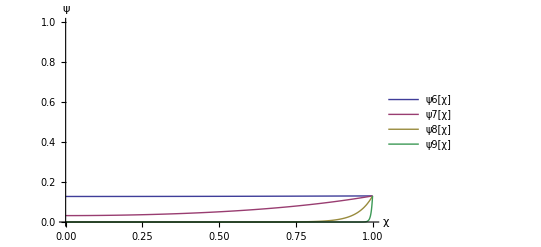

```mathematica
Plot[{ψ6[χ,.3],ψ7[χ,.3],ψ8[χ,.3],ψ9[χ,.3]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ6[χ]", "ψ7[χ]","ψ8[χ]","ψ9[χ]"},PlotRange->{0,1}]
```

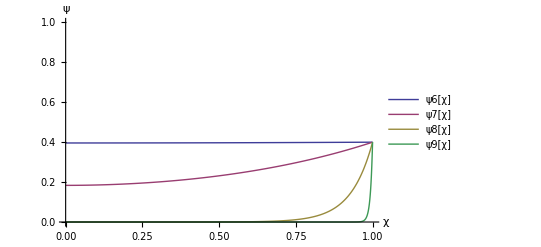

```mathematica
Plot[{ψ6[χ,1],ψ7[χ,1],ψ8[χ,1],ψ9[χ,1]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ6[χ]", "ψ7[χ]","ψ8[χ]","ψ9[χ]"},PlotRange->{0,1}]
```

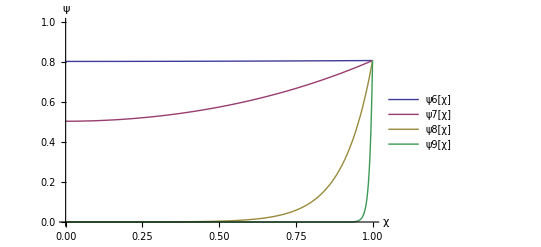

```mathematica
Plot[{ψ6[χ,10],ψ7[χ,10],ψ8[χ,10],ψ9[χ,10]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ6[χ]", "ψ7[χ]","ψ8[χ]","ψ9[χ]"},PlotRange->{0,1}]
```

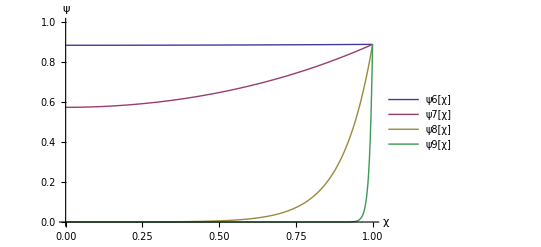

```mathematica
Plot[{ψ6[χ,100],ψ7[χ,100],ψ8[χ,100],ψ9[χ,100]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ6[χ]", "ψ7[χ]","ψ8[χ]","ψ9[χ]"},PlotRange->{0,1}]
```

```mathematica
For considerations:
```

```mathematica
-The Thiele modulus is corrected for the reversibility of the reaction.  In the large k limit, the differential equation collapses into the irreverisble case.  Otherwise, the Thielee modulus decreases as k decreases.  This decrease in the Thiele modulus decreases the effectiveness factor in this case.
```

```mathematica
Next, observing the effectiveness factors:
```

```mathematica
η1=Tanh[ϕ1]/ϕ1
```

0.99668

```mathematica
η2=N[Tanh[ϕ2]/ϕ2,3]
```

0.762

```mathematica
η3=N[Tanh[ϕ3]/ϕ3,3]
```

0.1

```mathematica
η4=N[Tanh[ϕ4]/ϕ4,3]
```

0.01

```mathematica
These values are heavily dependent upon the Thiele modulus, indicating that the irreversible reaction is  significantly diffusion limited for the third and fourth cases.  A high Thiele modulus indicates that the concentration changes occuring in the system are occuring at the reactions rate limitations.  While a small value indicated that these values are dominated by diffusion effects.
```

```mathematica
For the reversible case:
```

```mathematica
η6[k_]=Tanh[ϕ6[k]]/ϕ6[k]
```

(10. Tanh[0.1 √((1+k)/k)])/(√((1+k)/k))

```mathematica
η7[k_]=Tanh[ϕ7[k]]/ϕ7[k]
```

Tanh[√((1+k)/k)]/(√((1+k)/k))

```mathematica
η8[k_]=Tanh[ϕ8[k]]/ϕ8[k]
```

Tanh[10 √((1+k)/k)]/(10 √((1+k)/k))

```mathematica
η9[k_]=Tanh[ϕ9[k]]/ϕ9[k]
```

Tanh[100 √((1+k)/k)]/(100 √((1+k)/k))

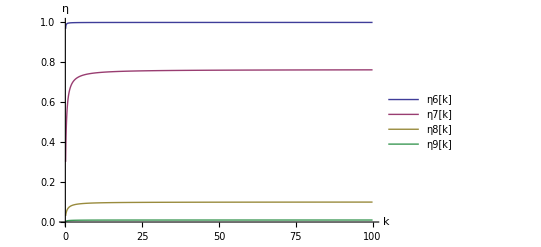

```mathematica
Plot[{η6[k],η7[k],η8[k],η9[k]},{k,.1,100},AxesLabel->{"k","η"},PlotLegends->{"η6[k]","η7[k]","η8[k]","η9[k]"}]
```

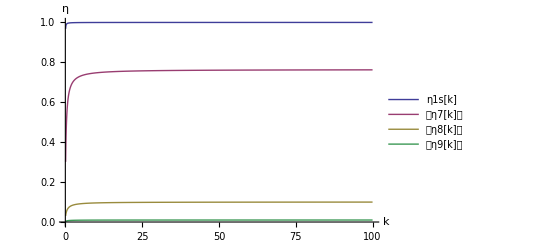

```mathematica
The effectiveness factor of the reversible case is somewhat rate constant dependent.  However, at k above ca. 10, this dependence is negligible.
```

```mathematica
coeffs2[k_]={η6[k],η7[k],η8[k],η9[k]}
```

{(10. Tanh[0.1 √((1+k)/k)])/(√((1+k)/k)),Tanh[√((1+k)/k)]/(√((1+k)/k)),Tanh[10 √((1+k)/k)]/(10 √((1+k)/k)),Tanh[100 √((1+k)/k)]/(100 √((1+k)/k))}

```mathematica
This table calculates the corrected moduluii associated with each of initial modulii paried with each of the k values.
```

```mathematica
TableForm[Table[N[coeffs2[k],3],{k,4}],TableHeadings->{{"ϕ6","ϕ7","ϕ8","ϕ9"},{"k=.1","k=1","k=10","k=100"}}]
```

| k=.1 | k=1 | k=10 | k=100
ϕ6 | 0.993386 | 0.628 | 0.0707 | 0.00707
ϕ7 | 0.99503 | 0.687 | 0.0816 | 0.00816
ϕ8 | 0.995579 | 0.71 | 0.0866 | 0.00866
ϕ9 | 0.995854 | 0.722 | 0.0894 | 0.00894

```mathematica
To adequately compare these two cases:
```

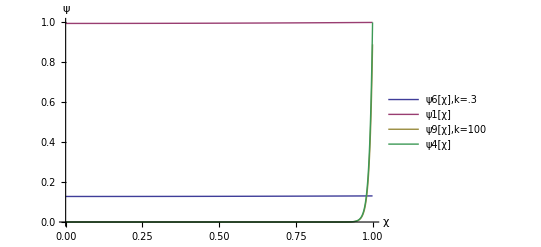

```mathematica
Plot[{ψ6[χ,.3],ψ1[χ],ψ9[χ,100],ψ4[χ]},{χ,0,1},AxesLabel->{"χ","ψ"},PlotLegends->{"ψ6[χ],k=.3", "ψ1[χ]","ψ9[χ],k=100","ψ4[χ]"},PlotRange->{0,1}]
```

```mathematica
Problem #3:
```

```mathematica
Part A:
```

```mathematica
Tb=773 (*K*);
```

```mathematica
kc=.5 (*m/min*);
```

```mathematica
λe=.5(*kJ/min-K*);
```

```mathematica
heat==-150 (*kJ/molO2*);
```

```mathematica
cAB=2(*mol/m3*);
```

```mathematica
cASmin=0
```

0

```mathematica
Clear[TMax]
```

```mathematica
Solve[TsMax-Ts==((-150)*kc*cAs)/λe,TsMax]
```

{{TsMax→473.}}

```mathematica
TSMax=473.(*K*)
```

473.

```mathematica
The maximum temperature difference is therefore(in degrees K):
```

```mathematica
TSMax-Ts
```

-300.

```mathematica
Rg=.008314 (*kJ/mol*K*);
```

```mathematica
The maximum rate occurs when cAS=0  and since cAB=2.  The following rate is in moles of O2/m^2 per minute:
```

```mathematica
RateMax=kc*(cAB-cASmin)
```

1.

```mathematica
Part B:
```

```mathematica
For a first-order reaction in a non-porous pellet, apply equation 6.4.1 (D&D p.219):
```

```mathematica
cAS[T_]=kc/(k[T]+kc)*cAB
```

1./(0.5+1000000 ⅇ^(-12027.9/T))

```mathematica
Apply equation to relate the observed rate and the temperature difference:
```

```mathematica
robs(-150)=λe(Tb-Ts)
```

```mathematica
Additionally, the observed rate is:
```

```mathematica
robs=kc(cAB-cAS[T])
```

```mathematica
Substituting gives:
```

```mathematica
Clear[Ts]
```

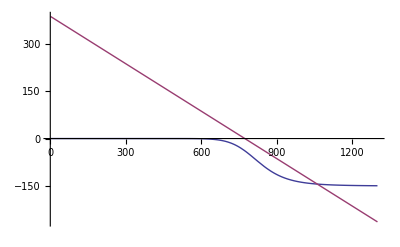

```mathematica
Plot[{kc(cAB-cAS[Ts])(-150),λe(Tb-Ts)},{Ts,1,1300}]
```

```mathematica
LHS[Ts_]=kc(cAB-cAS[Ts])(150);
```

```mathematica
RHS[Ts_]=λe(Tb-Ts);
```

```mathematica
LHS[1061]
```

143.967

```mathematica
RHS[1061]
```

-144.

```mathematica
Therefore the temperature at the surface is approxamately 1061 degrees Kelvin.
```

```mathematica
cAS[1043]
```

0.0969858

```mathematica
The actual rate under these conditions is therefore:
```

```mathematica
RateActual=kc*(cAB-cAS[1043])
```

0.951507

```mathematica
Problem 4:
```

```mathematica
Recall that the dependence of the effectiveness factor on Thiele modulus is given by:
```

```mathematica
ηf[ϕ_]=3/ϕ(1/Tanh[ϕ]-1/ϕ)
```

(3 (-1/ϕ+Coth[ϕ]))/ϕ

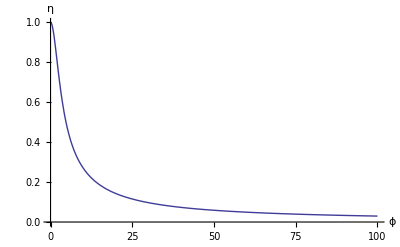

```mathematica
Plot[ηf[ϕ],{ϕ,0,100},PlotRange->{0,1},AxesLabel->{ϕ,η}]
```

```mathematica
The Thiele modulus is given by Eq 6.3.29(p.198):
```

```mathematica
ϕf=Rp*Sqrt[kf/dtaef];
```

```mathematica
The ratio of the Thiele modulii for two different particle sizes is:
```

```mathematica
ϕRatio=ϕa/ϕb
```

```mathematica
ϕRatio[Ra_,Rb_]=Ra/Rb;
```

```mathematica
ϕRatio[.03,.1]
```

0.3

```mathematica
ϕRatio[.8,.25]
```

3.2

```mathematica
ϕRatio[.2,.06]
```

3.33333

```mathematica
ϕRatio[.2,.02]
```

10.

```mathematica
ϕRatio[.2,.006]
```

33.3333

```mathematica
ϕRatio[.06,.02]
```

3.

```mathematica
ϕRatio[.06,.006]
```

10.

```mathematica
ϕRatio[.02,.006]
```

3.33333

```mathematica
The ratio of the effectivenesses for two given Thiele modulii is:
```

```mathematica
ηRatio[ϕf1_,ϕf2_]=ηf[ϕf1]/ηf[ϕf2];
```

```mathematica
ηRatio[phi2,phi1]
```

(phi1 (-1/phi2+Coth[phi2]))/(phi2 (-1/phi1+Coth[phi1]))

```mathematica
Then, evaluating this ratio as the second Thiele modulus having a specific value in terms of the first modulus which is ditated by the ratio of the radii:
```

```mathematica
ηRatio[.3*phi1,1*phi1]
```

(3.33333 (-3.33333/phi1+Coth[0.3 phi1]))/(-1/phi1+Coth[phi1])

```mathematica
Attempting to solve for the firs Thiele modulus utilizing Mathematica's built-in solver fails.  This is likely due to the ratio of cotangents messing up the solving algorithms.
```

```mathematica
Solve[ηRatio[.3*phi1,1*phi1]==3.2,phi1]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(3.33333 (-3.33333/phi1+Coth[0.3 phi1]))/(-1/phi1+Coth[phi1])==3.2,phi1]

```mathematica
NSolve[ηRatio[.3*phi1,1*phi1]==3.2,phi1]
```

NSolve[(3.33333 (-3.33333/phi1+Coth[0.3 phi1]))/(-1/phi1+Coth[phi1])==3.2,phi1]

```mathematica
The ratio of the observed rates is:
```

```mathematica
.80/.25
```

3.2

```mathematica
1.8/.25
```

7.2

```mathematica
2.5/.25
```

10.

```mathematica
Therefore the solutions are provided graphically, wherein the y=constant line comes from determining the ratio of the Thiele modulii as the ratios of the observed rates and the curve comes from the knowledge of the particle radii.
```

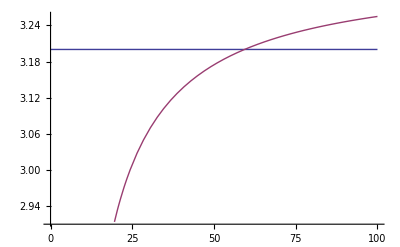

```mathematica
Plot[{3.2,ηRatio[.3*phi1,1*phi1]},{phi1,0,100}]
```

```mathematica
The solution to this system occurs at approxamately phi1=65.
```

```mathematica
Solve[65==.1*Sqrt[A],A]
```

{{A→422500.}}

```mathematica
A is k/D.
```

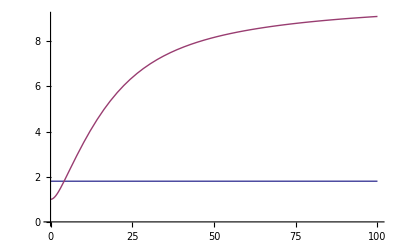

```mathematica
Plot[{1.8,ηRatio[.1*phi1,1*phi1]},{phi1,0,100}]
```

```mathematica
Solve[10==.1*Sqrt[A],A]
```

{{A→10000.}}

```mathematica
.003/.1
```

0.03

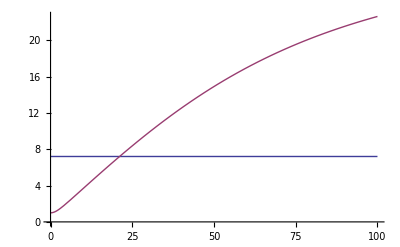

```mathematica
Plot[{7.2,ηRatio[.03*phi1,1*phi1]},{phi1,0,100}]
```

```mathematica
Solve[20==.1*Sqrt[A],A]
```

{{A→40000.}}

```mathematica
The average for k/Dtae is:
```

```mathematica
(40000+10000+422500)/3
```

157500

```mathematica
Calculate an exact value of each phi:
```

```mathematica
.1*157500
```

15750.

```mathematica
.03*157500
```

4725.

```mathematica
.01*157500
```

1575.

```mathematica
.003*157500
```

472.5

```mathematica
Calculate the exact value of each eta:
```

```mathematica
ηf[15750.]
```

0.000190464

```mathematica
ηf[4725.]
```

0.000634786

```mathematica
ηf[1575.]
```

0.00190355

```mathematica
ηf[472.5]
```

0.00633577

```mathematica
Calculate the exact k from  comparing the efficiency to the rate:
```

```mathematica
Solve[.25==0.00019046409674981101*k*.15,k]
```

{{k→8750.56}}

```mathematica
Solve[.80==0.0006347862601830856*k*.15,k]
```

{{k→8401.78}}

```mathematica
Solve[1.8==0.0019035525321239608*k*.15,k]
```

{{k→6304.}}

```mathematica
Solve[2.5==0.006335768875451416*k*.15,k]
```

{{k→2630.57}}

```mathematica
The average value of k (1/hr)is:
```

```mathematica
N[(8750+8401+6304+2630)/4,3]
```

6520.

```mathematica
The average value of D is:
```

```mathematica
k/D=157500
```

```mathematica
This is in cm^2/hr.
```

```mathematica
Solve[davg==6521.25`3./157500,davg]
```

{{davg→0.0414}}

```mathematica
davg=0.04140;
```

```mathematica
k=46 (*c,3/s-cm3 *)
```

```mathematica
Dtae=4.6*10^-3 (*cm2/s*)
```

```mathematica
The observed rate is given by:
```

```mathematica
robs=η*k*cASf
```

```mathematica
RAWdata={{.2,.25},{.06,.80},{.02,1.8},{.006,2.5}};
```

```mathematica
The large particle rates are split into one data set:
```

```mathematica
RAWdata1={{.2,.25},{.06,.80}};
```

```mathematica
The small particles are split into another data set:
```

```mathematica
RAWdata2={{.02,1.8},{.006,2.5}};
```

```mathematica
For the small particles the observed rate will be:
```

```mathematica
robs=k*cAs
```

```mathematica
For the large particles the observed rate will be:
```

```mathematica
robs=Rp*k^1.5*Dtae^.5*cAs
```

```mathematica
The following two cses will estimate k from the small particle data:
```

```mathematica
1.8/.15*2
```

24.

```mathematica
2.5/.15*2
```

33.3333

```mathematica
The average value is then computed(1/sec):
```

```mathematica
(12+16.67)
```

28.67

```mathematica
The next two cases will estimate Dtae from the large particle data:
```

```mathematica
(.80/(28)^1.5/.15/.06*2)^2
```

1.43973

```mathematica
(.25/(28)^1.5/.15/.2*2)^2
```

0.0126539

```mathematica
The average value is then(cm^2/hour):
```

```mathematica
(1.43+0.012)/2
```

0.721

```mathematica
nlm10=NonlinearModelFit[RAWdata,A*Exp[B*x],{A,B},x]
```

FittedModel[2.78629 ⅇ^(-20.5276 x)]

```mathematica
nlm10[x_]=2.786289244349898 ⅇ^(-20.527606952861277 x)
```

Set::write: Tag FittedModel in TagBox[FittedModel[TagBox[PanelBox[2.786289244349898` ⅇ^-20.527606952861277` x, Rule[FrameMargins, 5]], Rule[Editable, False]]], InterpretTemplate[Function[FittedModel[List[ is Protected.

2.78629 ⅇ^(-20.5276 x)

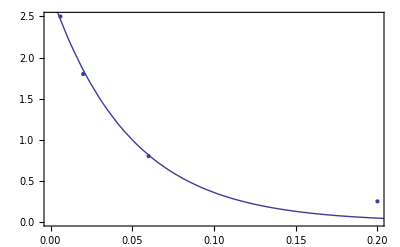

```mathematica
Show[ListPlot[RAWdata],Plot[nlm10[x],{x,-1,1}],Frame->True]
```

```mathematica
The regression line has a least squares fit of:
```

```mathematica
nlm["RSquared"]
```

0.995539

```mathematica
Part B:
```

```mathematica
From equation 6.3.50, for comparing a sphere to a cylinder:
```

```mathematica
Lp[Rp_]=Rp/(Rp/xp+2)
```

Rp/(2+1.66667 Rp)

```mathematica
Given dimensions:
```

```mathematica
xp=.6;
```

```mathematica
Rp1=.6/2;
```

```mathematica
Lp[Rp1]
```

0.12

```mathematica
Calculate the effectiveness factor with the generalized formula with the charicteristic legnth associated with a cylinder:
```

```mathematica
This should be about 10.
```

```mathematica
For the cylinder(6.3.48):
```

```mathematica
ϕcyl1=Lp[Rp1]*Sqrt[28.67/.7]
```

0.767973

```mathematica
ϕcyl2=Lp[Rp1]*Sqrt[46/4.6/10^-3]
```

12.

```mathematica
ηcyl[ϕ_]=Tanh[ϕ]/ϕ;
```

```mathematica
This eta should be about .1.
```

```mathematica
ηcyl[ϕcyl]
```

0.999952

```mathematica
ηcyl[ϕcyl2]
```

0.0833333

```mathematica
The rate for the cylinder should then be:
```

```mathematica
N[ηcyl[Lp[Rp1]*Sqrt[6.52*10^3/davg]]*60*.15,3]/360
```

0.000524971

```mathematica
ηcyl[Lp[Rp1]*Sqrt[k/Dtae]]
```

(8.33333 Tanh[0.12 √(k/Dtae)])/(√(k/Dtae))

```mathematica
Rate=ηcyl[ϕcyl]*28.67*cAs
```

48.2143

```mathematica
The units in the following line are mol/cm^2/hour
```

```mathematica
Rate=ηcyl[ϕcyl2]*46*.15
```

0.575

```mathematica
the units in the following line are mol.cm^2/second.
```

```mathematica
Rate/3600
```

0.000159722